

```mathematica
Graph[{UndirectedEdge[1,2]}]
```

```mathematica
RandomGraph[{2,2}]
```

RandomGraph::args: RandomGraph[{2,2}] called with invalid parameters.

RandomGraph[{2,2}]

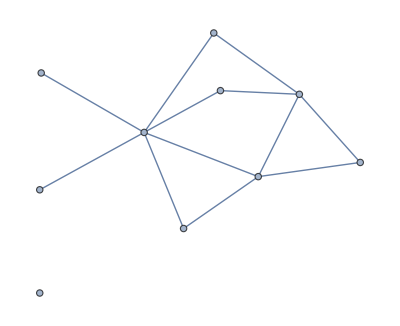

```mathematica
RandomGraph[{10,12}]
```

```mathematica
EdgeList[%12]
```

{1<->4,1<->7,2<->3,2<->6,2<->8,3<->9,4<->8,4<->9,5<->6,6<->8,6<->9,7<->10}

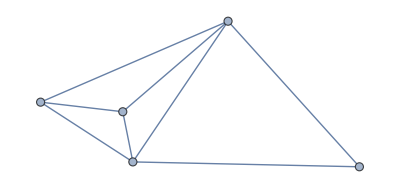

```mathematica
RandomGraph[SpatialGraphDistribution[5,0.5]]
```

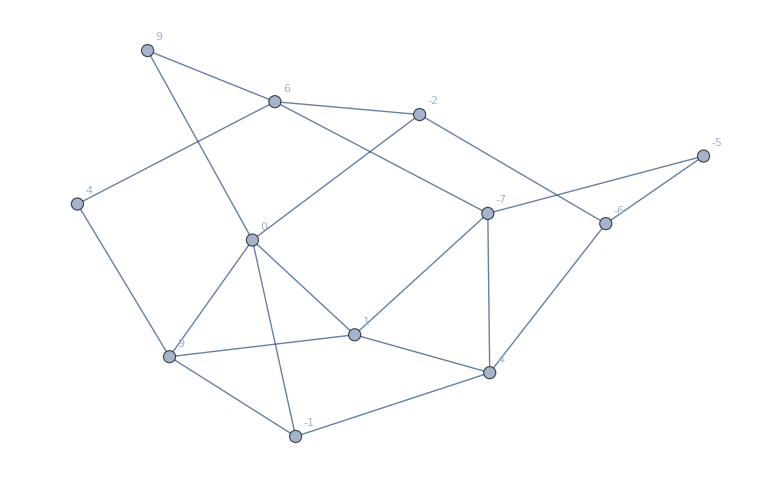

```mathematica
With[{v=12 (*vertices*),e=20 (*edges*)},NestWhile[RandomGraph[{v,e},DirectedEdges->False,VertexWeight->list9,VertexLabels->"VertexWeight"]&,Graph[{1<->1,2<->2}],Composition[Not,ConnectedGraphQ]]]
```

```mathematica
EdgeRules[%26]
```

{1→3,1→4,1→6,2→3,2→4,2→5,2→6,3→4,4→5,4→6,4→7,4→8,5→8,6→7}

```mathematica
5+4+1+4+5+0+0+3+4+4-3-2
```

25

```mathematica
20-12+1
```

9

```mathematica
list9=Table[RandomInteger[{-9,9}],{i,1,12}]
Sum[list9[[i]],{i,1,12}]
```

{-6,6,1,9,-2,0,9,-1,4,4,-5,-7}

12

```mathematica
list10={4,6,5,-3,-5}
Sum[list10[[i]],{i,1,5}]
```

{4,6,5,-3,-5}

7

```mathematica
{4,6,5,-3,-5}
```

{4,6,5,-3,-5}

```mathematica
10-5+1
```

6

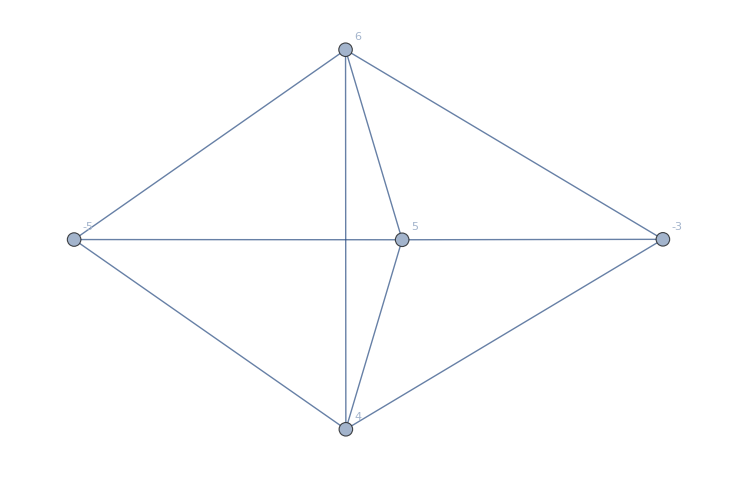

```mathematica
With[{v=5(*vertices*),e=9 (*edges*)},NestWhile[RandomGraph[{v,e},DirectedEdges->False,VertexWeight->list10,VertexLabels->"VertexWeight"]&,Graph[{1<->1,2<->2}],Composition[Not,ConnectedGraphQ]]]
```

```mathematica
list11={3,5,4,-3,-1,0}
Sum[list11[[i]],{i,1,6}]
9-5+1
```

{3,5,4,-3,-1,0}

8

5

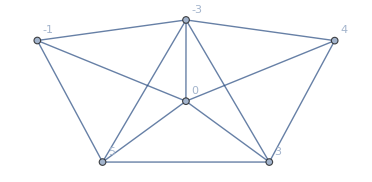

```mathematica
With[{v=6(*vertices*),e=12 (*edges*)},NestWhile[RandomGraph[{v,e},DirectedEdges->False,VertexWeight->list11,VertexLabels->"VertexWeight"]&,Graph[{1<->3,2<->4}],Composition[Not,ConnectedGraphQ]]]
```

```mathematica
list12={-1,-1,-2,2,2,5}
Sum[list12[[i]],{i,1,6}]
```

{-1,-1,-2,2,2,5}

5

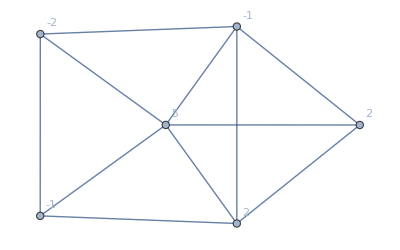

```mathematica
With[{v=6(*vertices*),e=11 (*edges*)},NestWhile[RandomGraph[{v,e},DirectedEdges->False,VertexWeight->list12,VertexLabels->"VertexWeight"]&,Graph[{1<->3,2<->4}],Composition[Not,ConnectedGraphQ]]]
```